```mathematica
ClearAll["Global`*"]
```

```mathematica
streak[x_, pAgain_] := If[x==-1,RandomChoice[{pAgain, 1-pAgain}-> {-1, 1}], RandomChoice[{1-pAgain, pAgain}-> {-1, 1}]]
ht[dep_, n_]:= NestList[streak[#, dep]&, -1, n]
```

```mathematica
streakBball[x_, pScore_, dep_]:= If[x=="score",RandomChoice[{pScore-dep,1-pScore+dep}-> {"score", "empty"}], RandomChoice[{1-pAgain, pAgain}-> {-1, 1}]]
```

```mathematica
randWalkDep[dep_, n_]:= Accumulate[NestList[streak[#, dep]&, -1, n]]
```

```mathematica
med = Table[ht[0.5, 1000], 10];
ext = Table[ht[0.525, 1000], 10];
medTwos1 = Map[SequenceCount[#, {1, 1}, Overlaps->True]&, med];
medTwos2 = Map[SequenceCount[#, {-1, -1}, Overlaps->True]&, med];
medTwos = medTwos1+medTwos2;
extTwos1 = Map[SequenceCount[#, {1, 1}, Overlaps->True]&, ext];
extTwos2 = Map[SequenceCount[#, {-1, -1}, Overlaps->True]&, ext];
extTwos = extTwos1+extTwos2;
Tally[MapThread[Greater, {extTwos, medTwos}]]
```

{{True,8},{False,2}}

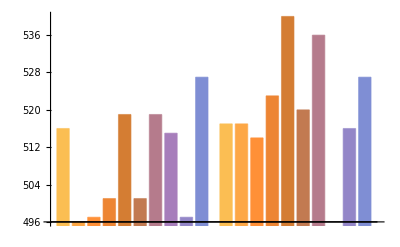

```mathematica
GraphicsRow[{ BarChart[{medTwos, extTwos}, PlotRange->{Automatic, {Min[medTwos], Max[extTwos]}}], 
}]
```

```mathematica
data =Import["/Users/erichegonzales/Projects/Probability/game_of_runs/Data/nba_2016_nfgs_nstreaks.csv", "Dataset", "HeaderLines"-> 1];
```

```mathematica
possStats201718 =Import["/Users/erichegonzales/Projects/Probability/game_of_runs/Data/all_stats_2017-18.csv", "Dataset", "HeaderLines"-> 1];
```

```mathematica
possStats =Import["/Users/erichegonzales/Projects/Probability/game_of_runs/Data/all_stats.csv", "Dataset", "HeaderLines"-> 1];
```

```mathematica
blazers2016 =Import["/Users/erichegonzales/Projects/Probability/game_of_runs/Data/blazers_2016_17.csv", "Dataset"];
```

```mathematica
simple = Map[If[StringContainsQ[#,"score"], "score", "empty"]&,blazers2016, {2}];
```

```mathematica
counts2 = Counts[Flatten[simple]]
```

```mathematica
pScore = N[counts2["score"] / Length[Flatten[simple]]]
pEmpty = N[counts2["empty"] / Length[Flatten[simple]]]
```

0.395104

0.604896

```mathematica
simpleTeam = Map[
If[StringContainsQ[ #, "POR"], 
If[StringContainsQ[#,"score"],
 "teamScore", "teamEmpty"],
If[StringContainsQ[#,"score"],
 "oppScore", "oppEmpty"]]&, blazers2016, {2}
];
```

Todo: Get the probabilities of all 4 then generate fake data, do test for fakes then test for real

```mathematica
counts = Counts[Flatten[simple]]
```

```mathematica
counts["teamScore"]
```

Missing[KeyAbsent,teamScore]

```mathematica
pTeamScore = N[counts["teamScore"] / (counts["teamScore"]+ counts["teamEmpty"])]
pOppScore = N[counts["oppScore"] / (counts["oppScore"]+ counts["oppEmpty"])]
pTeamEmpty =  1- pTeamScore
pOppEmpty = 1 - pOppScore
```

Missing[KeyAbsent,teamScore]/(Missing[KeyAbsent,teamEmpty]+Missing[KeyAbsent,teamScore])

Missing[KeyAbsent,oppScore]/(Missing[KeyAbsent,oppEmpty]+Missing[KeyAbsent,oppScore])

1-Missing[KeyAbsent,teamScore]/(Missing[KeyAbsent,teamEmpty]+Missing[KeyAbsent,teamScore])

1-Missing[KeyAbsent,oppScore]/(Missing[KeyAbsent,oppEmpty]+Missing[KeyAbsent,oppScore])

```mathematica
med4 =
```

```mathematica
Import["/Users/erichegonzales/Projects/Probability/game_of_runs/Data/blazers_2016_17_stats.csv", "Dataset", "HeaderLines"-> 1]
```

```mathematica
{a, b, c} = {1, 2, 3}
```

```mathematica
a
```

```mathematica
getIndandCounts[]:=Module[{countNFGS, countNStreaks, i, output},
countNFGS = 0;
countNStreaks = 0;
output = {};
i = 1;
While[i<=Length[data],
While[countNFGS <= 1000&&i<=Length[data], countNFGS += data[All, "NFGS"][[i]]; countNStreaks+= data[All, "NSTREAKS_OF_TWO"][[i]]; i++];
AppendTo[output,{i, countNFGS, countNStreaks}];
{countNFGS, countNStreaks} = {0, 0}
];
output]
```

```mathematica
indandCounts =getIndandCounts[]
```

```mathematica
Map[{#[[2]]}&, {{1, 2}, {3, 4}}]
```

```mathematica
med = Map[ht[0.5, #[[2]]]&, test];
medTwos1 = Map[SequenceCount[#, {1, 1}, Overlaps->True]&, med];
medTwos2 = Map[SequenceCount[#, {-1, -1}, Overlaps->True]&, med];
medTwos = medTwos1+medTwos2
```

```mathematica
indandCounts[[All, 3]]
```

```mathematica
Length[medTwos]
```

```mathematica
Length[test]
```

```mathematica
≥
```

```mathematica
countNStreaks
```

```mathematica
countNFGS
```

```mathematica
test =Range[10];
count = 0;
```

```mathematica
Scan[count += # Append[test, #+ count]&, Range[10]]
```

```mathematica
test
```

```mathematica
test
```

```mathematica
count = 0;
Scan[count + #&, Range[10]]
```

```mathematica
0
```

0

```mathematica
Partition[Range[25], UpTo[10]]
```

```mathematica
Partition[data[All, "NFGS"], 1000]
```

```mathematica
realTwos= Map[Total, Partition[data[All, "NSTREAKS_OF_TWO"], UpTo[1000]]]
realN = Map[Total, Partition[data[All, "NFGS"], UpTo[1000]]]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[13742.,Total[UpTo[1000]]].

Partition[13742.,Total[UpTo[1000]]]

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[93601,Total[UpTo[1000]]].

Partition[93601,Total[UpTo[1000]]]

```mathematica
medThrees = Map[SequenceCount[#, {n_, n_, n_}, Overlaps->True]&, med];
extThrees =Map[SequenceCount[#, {n_, n_, n_}, Overlaps->True]&, ext];
```

```mathematica
medTwos = Map[SequenceCount[#, {n_, n_}, Overlaps->True]&, med];
extTwos =Map[SequenceCount[#, {n_, n_}, Overlaps->True]&, ext];
```

```mathematica
medFours = Map[SequenceCount[#, {n_, n_, n_, n_}, Overlaps->True]&, med];
extFours =Map[SequenceCount[#, {n_, n_, n_, n_}, Overlaps->True]&, ext];
```

```mathematica
BarChart[{medThrees, extThrees}, PlotRange->{Automatic, {Min[medThrees], Max[extThrees]}}],
BarChart[{medFours, extFours}, PlotRange->{Automatic, {Min[medFours], Max[extFours]}}]
```

```mathematica
Differences[randWalkDep[0.5], 1, 1]
```

```mathematica
Differences[randWalkDep[0.5, 10],1]
```

```mathematica
-2==0
```

```mathematica
Abs[-2]!= Abs[2]
```

```mathematica
Tally[{0,-2,-2,-2,0,2,0,0,0}, Abs[#1]== Abs[#2]&]
```

```mathematica
BarChart[Labeled@@@Reverse[{{0,5},{-2,3},{2,1}},2]]
```

```mathematica
Button["new data", medioc =  randWalkDep[0.5, 2000];extrem = randWalkDep[dep, 2000]],
```

```mathematica
Manipulate[Module[{medioc, extrem},
medioc  = randWalkDep[0.5, 10000];
extrem = randWalkDep[dep, 10000];
GraphicsColumn[{ 
ListLinePlot[Differences[medioc, d, differenceWindow], PlotRange-> {{0, 10000},{plotrange, -plotrange}},  PlotLabel-> "Independent Differences"],ListLinePlot[Differences[extrem, d, differenceWindow], PlotRange-> {{0, 10000},{plotrange, -plotrange}},PlotStyle->Orange, PlotLabel-> "Dependent Differences"]}]],
{{dep, 0.55, "dependent_p"}, 0.1, 0.9, 0.025},
 {{d, 1, "nth derivative"}, 1, 10, 1},
{{differenceWindow, 20}, 1, 50, 1},
{{plotrange, 15}, 2, 1000, 5 },
 SynchronousUpdating->False]
```

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.5,10000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.55,10000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.5,10000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.55,10000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.5,2000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.525,2000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.5,2000.],1.,20.] is not a list of numbers or pairs of numbers.

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[randWalkDep[0.525,2000.],1.,20.] is not a list of numbers or pairs of numbers.

```mathematica
ht[dep_, n_]:= NestList[streak[#, dep]&, -1, n]
```

```mathematica
randWalkDep[dep_, n_]:= Accumulate[NestList[streak[#, dep]&, -1, n]]
```